# Kelvin problem in 2-d plane strain

Define the relevant functions that are needed for integrating the response to a point force

```mathematica
(*Get["/Users/mallickrishg/Downloads/mathematica2matlab/mathematica2matlab/ToMatlab.m"]*)
Get["/Users/rishav/Documents/GitHub/mathematica2matlab/ToMatlab.m"]
```

```mathematica
x = xo - xs;
y = yo - ys;
C0 = 1/ (4 * Pi *(1-ν));
r = Sqrt[x^2 + y^2];
g = -C0 * Log[r];
gx = -C0*x/r^2;
gy = -C0*y/r^2;
gxy = 2*C0*x*y/r^4;
gxx = C0*(x^2 - y^2)/r^4;
gyy = -gxx;
ux = fx/(2*μ)*((3-4*ν)*g - x*gx) + fy/(2*μ)*(-y*gx) 
uy = fx/(2*μ)*(-x*gy) + fy/(2*μ)*((3-4*ν)*g -y*gy)
sxx = fx*(2*(1 - ν)*gx - x*gxx) + fy*(2*ν* gy - y*gxx);
syy = fx*(2*ν*gx - x*gyy) + fy * (2*(1 - ν)*gy - y*gyy);
sxy = fx*((1 - 2*ν)*gy - x*gxy) + fy*((1 - 2*ν)*gx - y*gxy);
```

-(fy (xo-xs) (-yo+ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fx ((xo-xs)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

-(fx (-xo+xs) (yo-ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fy ((yo-ys)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

```mathematica
ux0 = ReplaceAll[ux,{ys->0,yo->0}]
uy0 = ReplaceAll[uy,{ys->0,yo->0}]
```

(fx (1/(4 π (1-ν))-((3-4 ν) Log[√((xo-xs)^2)])/(4 π (1-ν))))/(2 μ)

-(fy (3-4 ν) Log[√((xo-xs)^2)])/(8 π μ (1-ν))

```mathematica
uxInt0 = Integrate[ux0,{xs,-1,1},Assumptions->{Im[xo]==0}]
uyInt0 = Integrate[uy0,{xs,-1,1},Assumptions->{Im[xo]==0}]
```

-(fx (2+1/2 (-3+4 ν) (-4-(-1+xo) Log[(-1+xo)^2]+(1+xo) Log[(1+xo)^2])))/(8 π μ (-1+ν))

(fy (-3+4 ν) (4-2 xo ArcTanh[(2 xo)/(1+xo^2)]+Log[1/((-1+xo^2)^2)]))/(16 π μ (-1+ν))

### First compute indefinite integral and then evaluate at the end points to get definite integral

```mathematica
UxIndef = Integrate[ux,xs,GeneratedParameters->C];
UxDef = ReplaceAll[UxIndef,{xs->1}]-ReplaceAll[UxIndef,{xs->-1}]//FullSimplify
```

-1/(16 π μ (-1+ν))(-16 fx (-1+ν)-8 fx (yo-ys) (-1+ν) ArcTan[(-1+xo)/(yo-ys)]+8 fx (yo-ys) (-1+ν) ArcTan[(1+xo)/(yo-ys)]+fx (-3+4 ν) Log[(-1+xo)^2+(yo-ys)^2]+(fy (-yo+ys)+fx xo (3-4 ν)) Log[1+(-2+xo) xo+(yo-ys)^2]+fx (-3+4 ν) Log[(1+xo)^2+(yo-ys)^2]+(fy (yo-ys)+fx xo (-3+4 ν)) Log[1+xo (2+xo)+(yo-ys)^2])

```mathematica
UyIndef = Integrate[uy,xs,GeneratedParameters->C];
UyDef = ReplaceAll[UyIndef,{xs->1}]-ReplaceAll[UyIndef,{xs->-1}]//FullSimplify
```

-1/(16 π μ (-1+ν))(-2 fy (3-4 ν) (-1+xo+(-yo+ys) ArcTan[(-1+xo)/(yo-ys)])+2 fy (3-4 ν) (1+xo+(-yo+ys) ArcTan[(1+xo)/(yo-ys)])+fy (-1+xo) (3-4 ν) Log[(-1+xo)^2+(yo-ys)^2]+fy (1+xo) (-3+4 ν) Log[(1+xo)^2+(yo-ys)^2]+(fy √(-(yo-ys)^2)+fx (-yo+ys)) Log[-1+xo-√(-(yo-ys)^2)]+(fx (yo-ys)-fy √(-(yo-ys)^2)) Log[1+xo-√(-(yo-ys)^2)]-(fx (yo-ys)+fy √(-(yo-ys)^2)) Log[-1+xo+√(-(yo-ys)^2)]+(fx (yo-ys)+fy √(-(yo-ys)^2)) Log[1+xo+√(-(yo-ys)^2)])

## Check numerical solution versus analytical solution

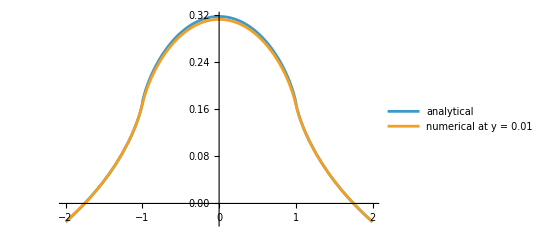

```mathematica
Plot[{ReplaceAll[uxInt0,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[UxDef,{fx->1,fy->0,μ->1,ν->0.25,ys->0,yo->0.01}]},{xo,-2,2},PlotLegends->{"analytical","numerical at y = 0.01"}]
```

## Plot analytical solutions for U_x and U_y (f_x = 1)

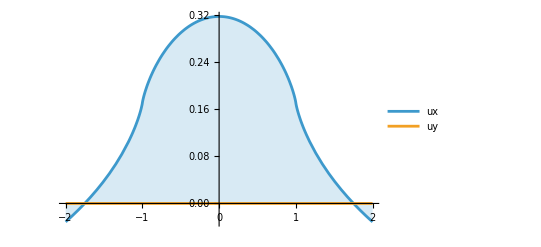

```mathematica
Plot[ {ReplaceAll[uxInt0,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[uyInt0,{fx->1,fy -> 0, μ->1,ν->0.25}]},{xo,-2,2},Filling->Axis,PlotLegends->{"ux","uy"}]
```

## Plot analytical solutions for U_x and U_y (f_y = -1)

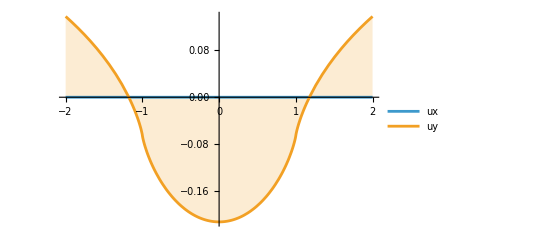

```mathematica
Plot[ {ReplaceAll[uxInt0,{fx -> 0,fy->-1, μ->1,ν->0.25}],ReplaceAll[uyInt0,{fx->0,fy -> -1, μ->1,ν->0.25}]},{xo,-2,2},Filling->Axis,PlotLegends->{"ux","uy"}]
```

## Plot numerical solution for U_x and U_y in 2-d

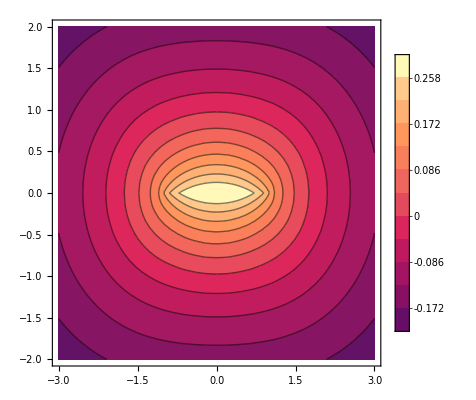

```mathematica
ContourPlot[ReplaceAll[UxDef,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->Automatic,Contours->11]
```

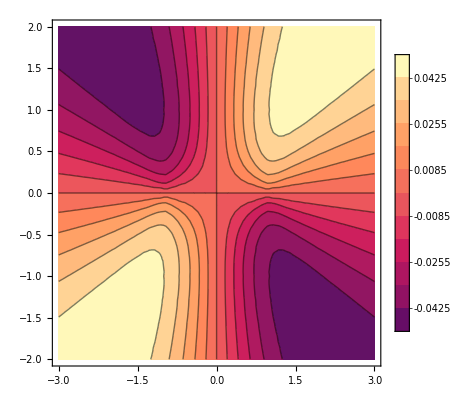

```mathematica
ContourPlot[ReplaceAll[UyDef,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->Automatic,Contours->11]
```

## Linearly varying force along line element 1. Displacements

```mathematica
(*uxLinIndefInt0 = Integrate[ReplaceAll[ux*(1 + 1/w*xs)/2,{ys->0}],xs,GeneratedParameters->C]//FullSimplify;*)uxLinIndefInt0 = Integrate[ReplaceAll[ux*(1 - 1/w*xs)/2,{ys->0}],xs,GeneratedParameters->C]//FullSimplify;
uxLinDefInt0 = (ReplaceAll[uxLinIndefInt0,{xs->w}] -  ReplaceAll[uxLinIndefInt0,{xs->-w}])//FullSimplify;
ux0 = Collect[%,{(w-xo)^2,yo^2 (5-4 ν)},FullSimplify]
ToMatlab[ux0]
```

(fx (w-xo)^2 (3-4 ν) Log[(w-xo)^2+yo^2])/(64 π w μ (-1+ν))+((w-xo) (-8 fx yo (-1+ν) (ArcTan[(w-xo)/yo]+ArcTan[(w+xo)/yo])+fy yo Log[(w-xo)^2+yo^2]))/(32 π w μ (-1+ν))+1/(64 π w μ (-1+ν))(4 w (-2 fy yo+fx xo (3-4 ν)+8 fx w (-1+ν))+yo^2 (4 fy (ArcTan[(w-xo)/yo]+ArcTan[(w+xo)/yo])+fx (-5+4 ν) Log[(w-xo)^2+yo^2])+(2 fy (-w+xo) yo+fx (3 (3 w-xo) (w+xo)+5 yo^2-4 ((3 w-xo) (w+xo)+yo^2) ν)) Log[(w+xo)^2+yo^2])

(1/64).*fx.*pi.^(-1).*w.^(-1).*(w+(-1).*xo).^2.*μ.^(-1).*(3+(-4).* ...
  ν).*((-1)+ν).^(-1).*log((w+(-1).*xo).^2+yo.^2)+(1/32).*pi.^(-1).* ...
  w.^(-1).*(w+(-1).*xo).*μ.^(-1).*((-1)+ν).^(-1).*((-8).*fx.*yo.*(( ...
  -1)+ν).*(atan((w+(-1).*xo).*yo.^(-1))+atan((w+xo).*yo.^(-1)))+fy.* ...
  yo.*log((w+(-1).*xo).^2+yo.^2))+(1/64).*pi.^(-1).*w.^(-1).*μ.^(-1) ...
  .*((-1)+ν).^(-1).*(4.*w.*((-2).*fy.*yo+fx.*xo.*(3+(-4).*ν)+8.*fx.* ...
  w.*((-1)+ν))+yo.^2.*(4.*fy.*(atan((w+(-1).*xo).*yo.^(-1))+atan((w+ ...
  xo).*yo.^(-1)))+fx.*((-5)+4.*ν).*log((w+(-1).*xo).^2+yo.^2))+(2.* ...
  fy.*((-1).*w+xo).*yo+fx.*(3.*(3.*w+(-1).*xo).*(w+xo)+5.*yo.^2+(-4) ...
  .*((3.*w+(-1).*xo).*(w+xo)+yo.^2).*ν)).*log((w+xo).^2+yo.^2));

```mathematica
(*uyLinIndefInt0 = Integrate[ReplaceAll[uy*(1 + 1/w*xs)/2,{ys->0}],xs,GeneratedParameters->C]//FullSimplify;*)
uyLinIndefInt0 = Integrate[ReplaceAll[uy*(1 - 1/w*xs)/2,{ys->0}],xs,GeneratedParameters->C]//FullSimplify;
uyLinDefInt0 = (ReplaceAll[uyLinIndefInt0,{xs->w}] -  ReplaceAll[uyLinIndefInt0,{xs->-w}])//FullSimplify;
uy0 = Collect[%,{fx,fy,(w-xo)^2,yo^2 (5-4 ν)},FullSimplify]
ToMatlab[uy0]
```

fx (-(yo (4 w-2 yo (ArcTan[(w-xo)/yo]+ArcTan[(w+xo)/yo])+(-w+xo) Log[(w-xo)^2+yo^2]))/(32 π w μ (-1+ν))+((w-xo) yo Log[w^2+2 w xo+xo^2+yo^2])/(32 π w μ-32 π w μ ν))+fy (-((w-xo) yo (-1+2 ν) (ArcTan[(w-xo)/yo]+ArcTan[(w+xo)/yo]))/(8 π w μ (-1+ν))+((w-xo)^2 (3-4 ν) Log[(w-xo)^2+yo^2])/(64 π w μ (-1+ν))+(4 w (2 w-xo) (-3+4 ν)+yo^2 (-1+4 ν) Log[(w-xo)^2+yo^2]+(3 (3 w-xo) (w+xo)+yo^2-4 ((3 w-xo) (w+xo)+yo^2) ν) Log[(w+xo)^2+yo^2])/(64 π w μ (-1+ν)))

fx.*((-1/32).*pi.^(-1).*w.^(-1).*yo.*μ.^(-1).*((-1)+ν).^(-1).*(4.* ...
  w+(-2).*yo.*(atan((w+(-1).*xo).*yo.^(-1))+atan((w+xo).*yo.^(-1)))+ ...
  ((-1).*w+xo).*log((w+(-1).*xo).^2+yo.^2))+(w+(-1).*xo).*yo.*(32.* ...
  pi.*w.*μ+(-32).*pi.*w.*μ.*ν).^(-1).*log(w.^2+2.*w.*xo+xo.^2+yo.^2) ...
  )+fy.*((-1/8).*pi.^(-1).*w.^(-1).*(w+(-1).*xo).*yo.*μ.^(-1).*((-1) ...
  +ν).^(-1).*((-1)+2.*ν).*(atan((w+(-1).*xo).*yo.^(-1))+atan((w+xo) ...
  .*yo.^(-1)))+(1/64).*pi.^(-1).*w.^(-1).*(w+(-1).*xo).^2.*μ.^(-1).* ...
  (3+(-4).*ν).*((-1)+ν).^(-1).*log((w+(-1).*xo).^2+yo.^2)+(1/64).* ...
  pi.^(-1).*w.^(-1).*μ.^(-1).*((-1)+ν).^(-1).*(4.*w.*(2.*w+(-1).*xo) ...
  .*((-3)+4.*ν)+yo.^2.*((-1)+4.*ν).*log((w+(-1).*xo).^2+yo.^2)+(3.*( ...
  3.*w+(-1).*xo).*(w+xo)+yo.^2+(-4).*((3.*w+(-1).*xo).*(w+xo)+yo.^2) ...
  .*ν).*log((w+xo).^2+yo.^2)));

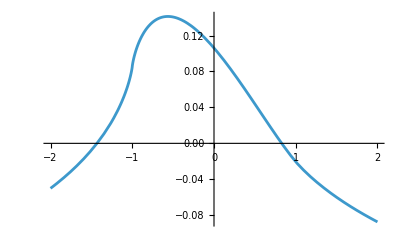

```mathematica
Plot[ReplaceAll[uy0,{fx->1,fy->1,w->1,μ->1,ν->0.25,yo->0.00001}],{xo,-2,2}]
```

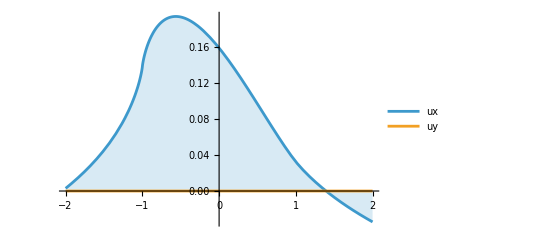

```mathematica
Plot[ {ReplaceAll[uxLinDefInt0,{fx -> 1,fy->0, μ->1,ν->0.25,w->1,Subscript[a, 0]->1,Subscript[a, 1]->1,yo->0.00001}],ReplaceAll[uyLinDefInt0,{fx -> 1,fy->0, μ->1,ν->0.25,w->1,Subscript[a, 0]->1,Subscript[a, 1]->1,yo->0.00001}]},{xo,-2,2},Filling->Axis,PlotLegends->{"ux","uy"}]
```

## 2. Stresses

```mathematica
sxyLinIndefInt0 = Integrate[ReplaceAll[sxy*(1 -1/w*xs)/2,{ys->0}],xs,GeneratedParameters->C]//FullSimplify;
sxxLinIndefInt0 = Integrate[ReplaceAll[sxx*(1 -1/w*xs)/2,{ys->0}],xs,GeneratedParameters->C]//FullSimplify;
syyLinIndefInt0 = Integrate[ReplaceAll[syy*(1 -1/w*xs)/2,{ys->0}],xs,GeneratedParameters->C]//FullSimplify;
```

```mathematica
sxyLinDefInt0 = ReplaceAll[sxyLinIndefInt0,{xs->w}] -  ReplaceAll[sxyLinIndefInt0,{xs->-w}]//FullSimplify;
sxxLinDefInt0 = ReplaceAll[sxxLinIndefInt0,{xs->w}] -  ReplaceAll[sxxLinIndefInt0,{xs->-w}]//FullSimplify;
syyLinDefInt0 = ReplaceAll[syyLinIndefInt0,{xs->w}] -  ReplaceAll[syyLinIndefInt0,{xs->-w}]//FullSimplify;
```

```mathematica
sxy0 = Collect[sxyLinDefInt0,{fx,fy},FullSimplify]
ToMatlab[sxy0]
```

-(fx ((4 w (w+xo) yo)/((w+xo)^2+yo^2)+4 (w-xo) (-1+ν) ArcTan[(w-xo)/yo]+4 (w-xo) (-1+ν) ArcTan[(w+xo)/yo]-yo (-3+2 ν) (Log[(w-xo)^2+yo^2]-Log[(w+xo)^2+yo^2])))/(16 π w (-1+ν))-(fy (-(4 w (w+xo)^2)/((w+xo)^2+yo^2)+8 w ν-4 yo ν ArcTan[(w-xo)/yo]-4 yo ν ArcTan[(w+xo)/yo]+(-w+xo) (-1+2 ν) (Log[(w-xo)^2+yo^2]-Log[(w+xo)^2+yo^2])))/(16 π w (-1+ν))

(-1/16).*fx.*pi.^(-1).*w.^(-1).*((-1)+ν).^(-1).*(4.*w.*(w+xo).* ...
  yo.*((w+xo).^2+yo.^2).^(-1)+4.*(w+(-1).*xo).*((-1)+ν).*atan((w+( ...
  -1).*xo).*yo.^(-1))+4.*(w+(-1).*xo).*((-1)+ν).*atan((w+xo).*yo.^( ...
  -1))+(-1).*yo.*((-3)+2.*ν).*(log((w+(-1).*xo).^2+yo.^2)+(-1).*log( ...
  (w+xo).^2+yo.^2)))+(-1/16).*fy.*pi.^(-1).*w.^(-1).*((-1)+ν).^(-1) ...
  .*((-4).*w.*(w+xo).^2.*((w+xo).^2+yo.^2).^(-1)+8.*w.*ν+(-4).*yo.* ...
  ν.*atan((w+(-1).*xo).*yo.^(-1))+(-4).*yo.*ν.*atan((w+xo).*yo.^(-1) ...
  )+((-1).*w+xo).*((-1)+2.*ν).*(log((w+(-1).*xo).^2+yo.^2)+(-1).* ...
  log((w+xo).^2+yo.^2)));

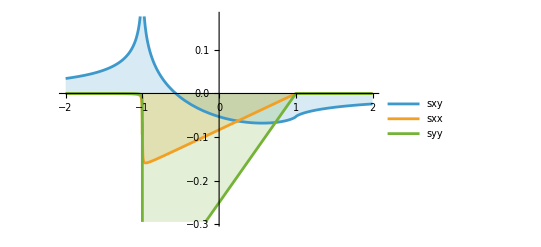

```mathematica
Plot[ {ReplaceAll[sxyLinDefInt0,{fx -> 0,fy->1, μ->1,ν->0.25,w->1,Subscript[a, 0]->-1,Subscript[a, 1]->1,yo->0.001}],ReplaceAll[sxxLinDefInt0,{fx -> 0,fy->1, μ->1,ν->0.25,w->1,Subscript[a, 0]->-1,Subscript[a, 1]->1,yo->0.001}],
ReplaceAll[syyLinDefInt0,{fx -> 0,fy->1, μ->1,ν->0.25,w->1,Subscript[a, 0]->-1,Subscript[a, 1]->1,yo->0.001}]},
{xo,-2,2},Filling->Axis,PlotLegends->{"sxy","sxx","syy"}]
```

## Derive and plot both basis functions

```mathematica
uxLinIndefInt0 = Integrate[ReplaceAll[ux*(1 + 1/w*xs)/2,{ys->0}],xs,GeneratedParameters->C]//FullSimplify;
uxLinDefInt0 = (ReplaceAll[uxLinIndefInt0,{xs->w}] -  ReplaceAll[uxLinIndefInt0,{xs->-w}])//FullSimplify;
ux1 = Collect[%,{(w-xo)^2,yo^2 (5-4 ν)},FullSimplify];
uyLinIndefInt0 = Integrate[ReplaceAll[uy*(1 + 1/w*xs)/2,{ys->0}],xs,GeneratedParameters->C]//FullSimplify;
uyLinDefInt0 = (ReplaceAll[uyLinIndefInt0,{xs->w}] -  ReplaceAll[uyLinIndefInt0,{xs->-w}])//FullSimplify;
uy1= Collect[%,{fx,fy,(w-xo)^2,yo^2 (5-4 ν)},FullSimplify];

uxLinIndefInt0 = Integrate[ReplaceAll[ux*(1 - 1/w*xs)/2,{ys->0}],xs,GeneratedParameters->C]//FullSimplify;
uxLinDefInt0 = (ReplaceAll[uxLinIndefInt0,{xs->w}] -  ReplaceAll[uxLinIndefInt0,{xs->-w}])//FullSimplify;
ux2 = Collect[%,{(w-xo)^2,yo^2 (5-4 ν)},FullSimplify]
uyLinIndefInt0 = Integrate[ReplaceAll[uy*(1 - 1/w*xs)/2,{ys->0}],xs,GeneratedParameters->C]//FullSimplify;
uyLinDefInt0 = (ReplaceAll[uyLinIndefInt0,{xs->w}] -  ReplaceAll[uyLinIndefInt0,{xs->-w}])//FullSimplify;
uy2 = Collect[%,{fx,fy,(w-xo)^2,yo^2 (5-4 ν)},FullSimplify];
```

(fx (w-xo)^2 (3-4 ν) Log[(w-xo)^2+yo^2])/(64 π w μ (-1+ν))+((w-xo) (-8 fx yo (-1+ν) (ArcTan[(w-xo)/yo]+ArcTan[(w+xo)/yo])+fy yo Log[(w-xo)^2+yo^2]))/(32 π w μ (-1+ν))+1/(64 π w μ (-1+ν))(4 w (-2 fy yo+fx xo (3-4 ν)+8 fx w (-1+ν))+yo^2 (4 fy (ArcTan[(w-xo)/yo]+ArcTan[(w+xo)/yo])+fx (-5+4 ν) Log[(w-xo)^2+yo^2])+(2 fy (-w+xo) yo+fx (3 (3 w-xo) (w+xo)+5 yo^2-4 ((3 w-xo) (w+xo)+yo^2) ν)) Log[(w+xo)^2+yo^2])

```mathematica
fxval=0.0;
fyval=1.0;
p1=ContourPlot[ReplaceAll[ux1,{fx->fxval,fy->fyval,μ->1,ν->0.25,w->1}],{xo,-2,2},{yo,-2,2},PlotLegends->Automatic,Contours->21,ColorFunction->"RedBlueTones"];
p2=ContourPlot[ReplaceAll[uy1,{fx->fxval,fy->fyval,μ->1,ν->0.25,w->1}],{xo,-2,2},{yo,-2,2},PlotLegends->Automatic,Contours->21,ColorFunction->"RedBlueTones"];
p3=ContourPlot[ReplaceAll[ux2,{fx->fxval,fy->fyval,μ->1,ν->0.25,w->1}],{xo,-2,2},{yo,-2,2},PlotLegends->Automatic,Contours->21,ColorFunction->"RedBlueTones"];
p4=ContourPlot[ReplaceAll[uy2,{fx->fxval,fy->fyval,μ->1,ν->0.25,w->1}],{xo,-2,2},{yo,-2,2},PlotLegends->Automatic,Contours->21,ColorFunction->"RedBlueTones"];
(*combine into a 2x2 grid*)
GraphicsGrid[{{p1,p2},{p3,p4}},Spacings->{0.5,0.5}]
```

-Graphics-